```mathematica
DataToAssociation[filename_] := 
Module[{},
data = Import[FileNameJoin[{NotebookDirectory[], filename}],"Table"];
transpose = Transpose[data];
timeData=Transpose[Rest[transpose]/. minutes_Integer:>TimeObject[{Quotient[minutes,100],Mod[minutes,100],0}]];
timeDiffTable = Table[Table[timeData[[All,j]][[i]]-timeData[[All,j]][[i-1]], {i, 2, Length[timeData]}], {j, 1, Length[Transpose[timeData]]}];
maxModeTimes = Table[Max[Commonest[timeDiffTable[[All, i]]]], {i, 1, Length[timeDiffTable[[1]]]}];
stopPairs = Table[List[First[transpose][[i-1]],First[transpose][[i]]], {i, 2, Length[maxModeTimes]+1}];
association = Association[Table[stopPairs[[i]]->maxModeTimes[[i]], {i, 1, Length[stopPairs]}]];
waiting = Association[Table[Keys[association][[i]]->
If[
(StringTake[Keys[association][[i]][[1]], -4] == "_arr" && StringTake[Keys[association][[i]][[2]], -4] == "_dep") ,
association[[Key[Keys[association][[i]]]]], Quantity[0, "Minutes"]],
{i, 1, Length[Keys[association]]}]];
travelTimeAssociation = Module[{cleaned},
cleaned = Association[];
i = 0;
While[i <Length[association],
i++;
If[waiting[[i]]==0 Quantity[, "Minutes"] && (StringTake[Keys[association][[i]][[1]], -4] == "_dep" || StringTake[Keys[association][[i]][[2]], -4] == "_arr"),
If[StringTake[Keys[association][[i]][[1]], -4] == "_dep",
AppendTo[cleaned, List[StringDrop[Keys[association][[i]][[1]], -4],Keys[association][[i]][[2]]]-> association[[Key[Keys[association][[i]]]]]],
AppendTo[cleaned, List[Keys[association][[i]][[1]],StringDrop[Keys[association][[i]][[2]], -4]]-> association[[Key[Keys[association][[i]]]]]]
],
If [waiting[[i]]==0 Quantity[, "Minutes"],
cleaned[Keys[association][[i]]] = association[[Key[Keys[association][[i]]]]],
Nothing[]],
Nothing[]];
];
cleaned
];

allStops = List[];
AppendTo[allStops, Keys[travelTimeAssociation][[1]][[1]]];
Do[AppendTo[allStops, x[[2]]],
{x, Keys[travelTimeAssociation]}
];
(*List[travelTimeAssociation, waiting, allStops]*)
travelTimeAssociation
];

SharedStops[route1_, route2_] := Intersection[Stops[route1], Stops[route2]];
```

```mathematica
x_⊕y_:=Max[x,y]
```

```mathematica
x_ ⊗y_:=x+y
```

```mathematica
mplus[x_,y_]:=MapThread[Max,{x,y}, 2]
```

```mathematica
mtimes[x_,y_]:=Inner[Plus,x,y,Max]
```

```mathematica
mpower[x_,p_]:= Module[{res},
If[p>=1,
res = x,
res = EMatrix[Length[x]]];
For[i = 2, i<=p, i++,
res = mtimes[res, x]
];
res
]
```

```mathematica
scalarplus[x_,y_]:=Outer[Max,{x},y]
```

```mathematica
eps=-Infinity
```

-∞

```mathematica
EpsilonMatrix[n_] := Table[Table[eps, {col, 1, n}], {row, 1, n}]
(* Returns an n x n matrix filled with Epsilon *)
```

```mathematica
EMatrix[n_]:= Table[Table[If[col == row, 0, eps], {col, 1, n}], {row, 1, n}]
(* Returns an n x n identity matrix *)
```

```mathematica
MakeNicePlaceName[rn_, s1_, s2_] :=ToString[StringJoin["p:",rn,":", s1, "+", s2]]
(* returns a formatted place name *)
```

```mathematica
MakeNiceTransitionName[rn_,q_] := ToString[StringJoin["q:",rn,":", q]]
(* returns a formatted transition name *)
```

```mathematica
MergeDirections[forward_, reverse_] := Module[{f, r, merged, nk, xS, start, end},
(* merges the forward and backward (arbitary) directions of a bus route *)
f = DataToAssociation[forward];
start = Keys[f][[1]][[1]];
r = DataToAssociation[reverse];
end = Keys[r][[1]][[1]];

Do[
nk ={If[x[[1]] ==start,start,StringJoin[x[[1]], "_fwd"]], If[x[[2]] ==end,end,StringJoin[x[[2]], "_fwd"]]};
f[nk] = f[x];
f[x] =.,
{x, Keys[f]}
];

Do[
nk ={If[x[[1]] ==end,end,StringJoin[x[[1]], "_rev"]], If[x[[2]] ==start,start,StringJoin[x[[2]], "_rev"]]};
r[nk] = r[x];
r[x] =.,
{x, Keys[r]}
];

merged = Join[f, r];
merged
]
```

```mathematica
GetTransitionStopName[transitionString_] := StringDrop[StringSplit[transitionString, ":"][[-1]],-4];
(* returns the transition name from a "nice" formatted transition *)

GetTransitionStop[transitionString_]:=StringSplit[transitionString, ":"][[-1]];
(* returns the transition stop, including route direction from a "nice" formatted transition *)
```

```mathematica
GetTransitionRoute[transitionString_] :=StringSplit[transitionString, ":"][[2]];(* returns the transition route number from a "nice" formatted transition *)
```

```mathematica
Algorithm821[lineDataFile_, routeNumbers_]:=
(*Line data file is a list of associations, where each asscoiation corresponds to a merged version of the TT association for the forward and backward journey of a given route. So each association represents a route*)
Module[{TAPsFromRoute, Synchronization, NumberRoutes, cycleTime},
cycleTime =60 Quantity[, "Minutes"];

NumberRoutes[] := Module[{indexedAssociations},
(* returns an association with route number as key and travel time associations (route data) as values *)
indexedAssociations = Association[];
For[i=1,i<=Length[routeNumbers], i++,
indexedAssociations[routeNumbers[[i]]]= lineDataFile[[i]];
];
indexedAssociations
];

TAPsFromRoute[routeNumber_, routeAssociation_] :=Module[{startStop, endStop, cumulativeTime,nextStopCumulativeTime, modCumulative, modNextCumulative,tokens, finalHoldingTime, transitions, places, arcs},
(* returns the transitions, arcs, and place of an individual route *)
transitions = List[];
places = Association[];
arcs = List[];
startStop = Keys[routeAssociation][[1]][[1]];
endStop = Keys[routeAssociation][[-1]][[1]];
AppendTo[transitions,MakeNiceTransitionName[routeNumber, startStop]];
cumulativeTime = 0 Quantity[, "Minutes"];
Do[
AppendTo[transitions,MakeNiceTransitionName[routeNumber, pair[[2]]]];
nextStopCumulativeTime =cumulativeTime + routeAssociation[[Key[pair]]];
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(routeAssociation[[Key[pair]]] + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places,  MakeNicePlaceName[routeNumber, pair[[1]],pair[[2]]]->List[routeAssociation[[Key[pair]]], tokens]];
cumulativeTime = nextStopCumulativeTime;
AppendTo[arcs, MakeNiceTransitionName[routeNumber, pair[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[routeNumber, pair[[2]]]];
,
{pair, Keys[routeAssociation][[1;;-2]]}
];
finalHoldingTime =routeAssociation[[Key[List[endStop, StringReplace[startStop, {"fwd"->"rev"}]]]]];
nextStopCumulativeTime =cumulativeTime + finalHoldingTime;
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(finalHoldingTime + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places, MakeNicePlaceName[routeNumber,endStop, startStop]->List[finalHoldingTime, tokens] ]; (*make sure this is indeed the last one*)
AppendTo[arcs, MakeNiceTransitionName[routeNumber, endStop]->MakeNicePlaceName[routeNumber, endStop, startStop]];
AppendTo[arcs, MakeNicePlaceName[routeNumber, endStop, startStop]->MakeNiceTransitionName[routeNumber, startStop]];
List[transitions, arcs, places]
];

Synchronization[routePlaces_] := Module[{arcs, places, indexedRoutes},
(* returns the arcs and places between routes with shared stops *)
indexedRoutes = NumberRoutes[];
arcs=List[];
places=Association[];
Do[
Do[
Do[
Do[
If[assoc1 != assoc2,
If[StringDrop[key1[[2]],-4]==StringDrop[key2[[2]],-4],
(* add arc from previous stop on origin line to new place *)
(* add arc from new place to shared stop on the other line *)
placeWeWant = MakeNicePlaceName[assoc2, key2[[1]], key2[[2]] ];
AppendTo[places, MakeNicePlaceName[StringJoin[assoc2, "->", assoc1], key2[[1]], key1[[2]]]->routePlaces[[placeWeWant]]];
AppendTo[arcs, MakeNiceTransitionName[assoc2,key2[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[assoc1, key1[[2]]]];,
Nothing[]
];
Nothing[]
];,
{key2,Keys[indexedRoutes[[Key[assoc2]]]]}
],
{key1,Keys[indexedRoutes[[Key[assoc1]]]]}
],
{assoc2,Keys[indexedRoutes]}
],
{assoc1,Keys[indexedRoutes]}
];
List[arcs, places]
];

transitions = List[];
places = Association[];
arcs = List[];

(* find transitions, arcs, and places for all routes *);
For[i=1, i<=Length[lineDataFile], i++,
temps= TAPsFromRoute[routeNumbers[[i]], lineDataFile[[i]]];
transitions = Join[transitions, temps[[1]]];
arcs = Join[arcs, temps[[2]]];
places = Join[places, temps[[3]]];
];

(* find arcs and places between routes *);
sync = Synchronization[places];
arcs = Join[arcs, sync[[1]]];
places = Join[places, sync[[2]]];

List[transitions, arcs, places]
]
```

```mathematica
AlgorithmYouJustDoIt[transitions_, arcs_, places_] := Module[{Main, GetPlaceBetween},
GetPlaceBetween[t1_, t2_] :=Module[{p},
If[
GetTransitionRoute[t1]==GetTransitionRoute[t2],

p =MakeNicePlaceName[GetTransitionRoute[t1], GetTransitionStop[t1], GetTransitionStop[t2]],

p = MakeNicePlaceName[StringJoin[GetTransitionRoute[t1], "->", GetTransitionRoute[t2]], GetTransitionStop[t1], GetTransitionStop[t2]]
];
p
];

Main[]:=Module[{maxTokens, p},
maxTokens = 0;
Do[
If[x[[2]]>maxTokens,
maxTokens=x[[2]],
Nothing[]
],
{x, places}];

matrices = List[];

For[m=0, m<=maxTokens, m++, 
matrix = List[];
Do[
row =List[];
Do[
p =GetPlaceBetween[j,i];
If[MemberQ[Keys[places], p],
p = places[[p]];
If[p[[2]]==m,
AppendTo[row, p[[1]]],
AppendTo[row, eps]
],
AppendTo[row, eps];
];,
{j, transitions}];
AppendTo[matrix, row];
,
{i, transitions}];
AppendTo[matrices, matrix];
];
matrices
];

Main[]
]
```

```mathematica
AlgorithmA0Star[A0_, lenTransitions_] :=Module[{R},
R =EMatrix[Length[A0]];
For[l=1, l<=lenTransitions, l=l+1,
R=mplus[R,mpower[A0, l]];
];
R
]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"]
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"]
```

<|{Wallacebrae_Road,Bodachra_Place_fwd}→7. min,{Bodachra_Place_fwd,North_Donside_Road_fwd}→7. min,{North_Donside_Road_fwd,School_Road_fwd}→7. min,{School_Road_fwd,Errol_Street_fwd}→5. min,{Errol_Street_fwd,Castle_Street_fwd}→5. min,{Castle_Street_fwd,Music_Hall_fwd}→5. min,{Music_Hall_fwd,Bridge_of_Dee_Court}→14. min,{Bridge_of_Dee_Court,Robert_Gordon_University_rev}→4. min,{Robert_Gordon_University_rev,Auchinyell_Gardens_rev}→8. min,{Auchinyell_Gardens_rev,Great_Western_Road_rev}→8. min,{Great_Western_Road_rev,Castle_Street_rev}→11. min,{Castle_Street_rev,Errol_Street_rev}→4. min,{Errol_Street_rev,School_Drive_rev}→5. min,{School_Drive_rev,Fraserfield_Gardens_rev}→7. min,{Fraserfield_Gardens_rev,Wallacebrae_Road}→13. min|>

<|{Golf_Links,Beach_Boulevard_fwd}→10. min,{Beach_Boulevard_fwd,St_Andrew's_Cathedral_fwd}→10. min,{St_Andrew's_Cathedral_fwd,Prince_Arthur_Street_fwd}→13. min,{Prince_Arthur_Street_fwd,Mastrick_Shops_fwd}→15. min,{Mastrick_Shops_fwd,Turning_Circle}→9. min,{Turning_Circle,Summerhill_Terrace_rev}→15. min,{Summerhill_Terrace_rev,Bridge_Street_rev}→15. min,{Bridge_Street_rev,Castle_Street_rev}→7. min,{Castle_Street_rev,Beach_Boulevard_rev}→6. min,{Beach_Boulevard_rev,Golf_Links}→14. min|>

```mathematica
TAPs=Algorithm821[{b1, b13}, {"1", "13"}]
```

{{q:1:Wallacebrae_Road,q:1:Bodachra_Place_fwd,q:1:North_Donside_Road_fwd,q:1:School_Road_fwd,q:1:Errol_Street_fwd,q:1:Castle_Street_fwd,q:1:Music_Hall_fwd,q:1:Bridge_of_Dee_Court,q:1:Robert_Gordon_University_rev,q:1:Auchinyell_Gardens_rev,q:1:Great_Western_Road_rev,q:1:Castle_Street_rev,q:1:Errol_Street_rev,q:1:School_Drive_rev,q:1:Fraserfield_Gardens_rev,q:13:Golf_Links,q:13:Beach_Boulevard_fwd,q:13:St_Andrew's_Cathedral_fwd,q:13:Prince_Arthur_Street_fwd,q:13:Mastrick_Shops_fwd,q:13:Turning_Circle,q:13:Summerhill_Terrace_rev,q:13:Bridge_Street_rev,q:13:Castle_Street_rev,q:13:Beach_Boulevard_rev},{q:1:Wallacebrae_Road→p:1:Wallacebrae_Road+Bodachra_Place_fwd,p:1:Wallacebrae_Road+Bodachra_Place_fwd→q:1:Bodachra_Place_fwd,q:1:Bodachra_Place_fwd→p:1:Bodachra_Place_fwd+North_Donside_Road_fwd,p:1:Bodachra_Place_fwd+North_Donside_Road_fwd→q:1:North_Donside_Road_fwd,q:1:North_Donside_Road_fwd→p:1:North_Donside_Road_fwd+School_Road_fwd,p:1:North_Donside_Road_fwd+School_Road_fwd→q:1:School_Road_fwd,q:1:School_Road_fwd→p:1:School_Road_fwd+Errol_Street_fwd,p:1:School_Road_fwd+Errol_Street_fwd→q:1:Errol_Street_fwd,q:1:Errol_Street_fwd→p:1:Errol_Street_fwd+Castle_Street_fwd,p:1:Errol_Street_fwd+Castle_Street_fwd→q:1:Castle_Street_fwd,q:1:Castle_Street_fwd→p:1:Castle_Street_fwd+Music_Hall_fwd,p:1:Castle_Street_fwd+Music_Hall_fwd→q:1:Music_Hall_fwd,q:1:Music_Hall_fwd→p:1:Music_Hall_fwd+Bridge_of_Dee_Court,p:1:Music_Hall_fwd+Bridge_of_Dee_Court→q:1:Bridge_of_Dee_Court,q:1:Bridge_of_Dee_Court→p:1:Bridge_of_Dee_Court+Robert_Gordon_University_rev,p:1:Bridge_of_Dee_Court+Robert_Gordon_University_rev→q:1:Robert_Gordon_University_rev,q:1:Robert_Gordon_University_rev→p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev,p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev→q:1:Auchinyell_Gardens_rev,q:1:Auchinyell_Gardens_rev→p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev,p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev→q:1:Great_Western_Road_rev,q:1:Great_Western_Road_rev→p:1:Great_Western_Road_rev+Castle_Street_rev,p:1:Great_Western_Road_rev+Castle_Street_rev→q:1:Castle_Street_rev,q:1:Castle_Street_rev→p:1:Castle_Street_rev+Errol_Street_rev,p:1:Castle_Street_rev+Errol_Street_rev→q:1:Errol_Street_rev,q:1:Errol_Street_rev→p:1:Errol_Street_rev+School_Drive_rev,p:1:Errol_Street_rev+School_Drive_rev→q:1:School_Drive_rev,q:1:School_Drive_rev→p:1:School_Drive_rev+Fraserfield_Gardens_rev,p:1:School_Drive_rev+Fraserfield_Gardens_rev→q:1:Fraserfield_Gardens_rev,q:1:Fraserfield_Gardens_rev→p:1:Fraserfield_Gardens_rev+Wallacebrae_Road,p:1:Fraserfield_Gardens_rev+Wallacebrae_Road→q:1:Wallacebrae_Road,q:13:Golf_Links→p:13:Golf_Links+Beach_Boulevard_fwd,p:13:Golf_Links+Beach_Boulevard_fwd→q:13:Beach_Boulevard_fwd,q:13:Beach_Boulevard_fwd→p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd,p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd→q:13:St_Andrew's_Cathedral_fwd,q:13:St_Andrew's_Cathedral_fwd→p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd,p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd→q:13:Prince_Arthur_Street_fwd,q:13:Prince_Arthur_Street_fwd→p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd,p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd→q:13:Mastrick_Shops_fwd,q:13:Mastrick_Shops_fwd→p:13:Mastrick_Shops_fwd+Turning_Circle,p:13:Mastrick_Shops_fwd+Turning_Circle→q:13:Turning_Circle,q:13:Turning_Circle→p:13:Turning_Circle+Summerhill_Terrace_rev,p:13:Turning_Circle+Summerhill_Terrace_rev→q:13:Summerhill_Terrace_rev,q:13:Summerhill_Terrace_rev→p:13:Summerhill_Terrace_rev+Bridge_Street_rev,p:13:Summerhill_Terrace_rev+Bridge_Street_rev→q:13:Bridge_Street_rev,q:13:Bridge_Street_rev→p:13:Bridge_Street_rev+Castle_Street_rev,p:13:Bridge_Street_rev+Castle_Street_rev→q:13:Castle_Street_rev,q:13:Castle_Street_rev→p:13:Castle_Street_rev+Beach_Boulevard_rev,p:13:Castle_Street_rev+Beach_Boulevard_rev→q:13:Beach_Boulevard_rev,q:13:Beach_Boulevard_rev→p:13:Beach_Boulevard_rev+Golf_Links,p:13:Beach_Boulevard_rev+Golf_Links→q:13:Golf_Links,q:13:Bridge_Street_rev→p:13->1:Bridge_Street_rev+Castle_Street_fwd,p:13->1:Bridge_Street_rev+Castle_Street_fwd→q:1:Castle_Street_fwd,q:13:Bridge_Street_rev→p:13->1:Bridge_Street_rev+Castle_Street_rev,p:13->1:Bridge_Street_rev+Castle_Street_rev→q:1:Castle_Street_rev,q:1:Errol_Street_fwd→p:1->13:Errol_Street_fwd+Castle_Street_rev,p:1->13:Errol_Street_fwd+Castle_Street_rev→q:13:Castle_Street_rev,q:1:Great_Western_Road_rev→p:1->13:Great_Western_Road_rev+Castle_Street_rev,p:1->13:Great_Western_Road_rev+Castle_Street_rev→q:13:Castle_Street_rev},<|p:1:Wallacebrae_Road+Bodachra_Place_fwd→{7. min,0},p:1:Bodachra_Place_fwd+North_Donside_Road_fwd→{7. min,0},p:1:North_Donside_Road_fwd+School_Road_fwd→{7. min,0},p:1:School_Road_fwd+Errol_Street_fwd→{5. min,0},p:1:Errol_Street_fwd+Castle_Street_fwd→{5. min,0},p:1:Castle_Street_fwd+Music_Hall_fwd→{5. min,0},p:1:Music_Hall_fwd+Bridge_of_Dee_Court→{14. min,0},p:1:Bridge_of_Dee_Court+Robert_Gordon_University_rev→{4. min,0},p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev→{8. min,1},p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev→{8. min,0},p:1:Great_Western_Road_rev+Castle_Street_rev→{11. min,0},p:1:Castle_Street_rev+Errol_Street_rev→{4. min,0},p:1:Errol_Street_rev+School_Drive_rev→{5. min,0},p:1:School_Drive_rev+Fraserfield_Gardens_rev→{7. min,0},p:1:Fraserfield_Gardens_rev+Wallacebrae_Road→{13. min,1},p:13:Golf_Links+Beach_Boulevard_fwd→{10. min,0},p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd→{10. min,0},p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd→{13. min,1},p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd→{15. min,1},p:13:Mastrick_Shops_fwd+Turning_Circle→{9. min,0},p:13:Turning_Circle+Summerhill_Terrace_rev→{15. min,1},p:13:Summerhill_Terrace_rev+Bridge_Street_rev→{15. min,1},p:13:Bridge_Street_rev+Castle_Street_rev→{7. min,0},p:13:Castle_Street_rev+Beach_Boulevard_rev→{6. min,0},p:13:Beach_Boulevard_rev+Golf_Links→{14. min,0},p:13->1:Bridge_Street_rev+Castle_Street_fwd→{7. min,0},p:13->1:Bridge_Street_rev+Castle_Street_rev→{7. min,0},p:1->13:Errol_Street_fwd+Castle_Street_rev→{5. min,0},p:1->13:Great_Western_Road_rev+Castle_Street_rev→{11. min,0}|>}

```mathematica
mtx =AlgorithmYouJustDoIt[TAPs[[1]], TAPs[[2]], TAPs[[3]]][[1]] // MatrixForm
```

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
7. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | 7. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 7. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | 5. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. min | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | 5. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 4. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 11. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. min | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 4. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 5. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. min
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 9. min | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. min | -∞ | -∞ | -∞ | -∞ | -∞ | 11. min | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. min | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 6. min | -∞)

```mathematica
A0 = {{eps, eps, eps, eps}, {1.5, eps, eps, eps}, {2,2,eps,eps}, {eps, eps, 2.5, eps}}
```

{{-∞,-∞,-∞,-∞},{1.5,-∞,-∞,-∞},{2,2,-∞,-∞},{-∞,-∞,2.5,-∞}}

```mathematica
AlgorithmA0Star[A0, 3]
```

{{0,-∞,-∞,-∞},{1.5,0,-∞,-∞},{3.5,2,0,-∞},{6.,4.5,2.5,0}}

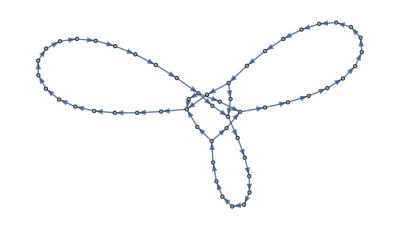

```mathematica
Graph[TAPs[[2]]]
```

PetriNetObject[…]

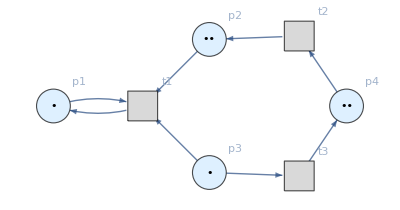

```mathematica
petriNetExample=ResourceFunction["MakePetriNet"][{p1,p2,p3,p4},{t1,t2,t3},{p1->t1,t1->p1,p2->t1,p3->t1,t2->p2,p3->t3,t3->p4,p4->t2},{1,2,1,2}]
petriNetExample["LabeledGraph"]
```

```mathematica
petriNet=Algorithm821[{b1, b13}, {"1", "13"}];
placesList=Keys[petriNet[[3]]];
transitionsList=petriNet[[1]];
arcsList=petriNet[[2]]
initialMarkings=#[[2]]&/@Values[petriNet[[3]]]
```

{q:1:Wallacebrae_Road→p:1:Wallacebrae_Road+Bodachra_Place_fwd,p:1:Wallacebrae_Road+Bodachra_Place_fwd→q:1:Bodachra_Place_fwd,q:1:Bodachra_Place_fwd→p:1:Bodachra_Place_fwd+North_Donside_Road_fwd,p:1:Bodachra_Place_fwd+North_Donside_Road_fwd→q:1:North_Donside_Road_fwd,q:1:North_Donside_Road_fwd→p:1:North_Donside_Road_fwd+School_Road_fwd,p:1:North_Donside_Road_fwd+School_Road_fwd→q:1:School_Road_fwd,q:1:School_Road_fwd→p:1:School_Road_fwd+Errol_Street_fwd,p:1:School_Road_fwd+Errol_Street_fwd→q:1:Errol_Street_fwd,q:1:Errol_Street_fwd→p:1:Errol_Street_fwd+Castle_Street_fwd,p:1:Errol_Street_fwd+Castle_Street_fwd→q:1:Castle_Street_fwd,q:1:Castle_Street_fwd→p:1:Castle_Street_fwd+Music_Hall_fwd,p:1:Castle_Street_fwd+Music_Hall_fwd→q:1:Music_Hall_fwd,q:1:Music_Hall_fwd→p:1:Music_Hall_fwd+Bridge_of_Dee_Court,p:1:Music_Hall_fwd+Bridge_of_Dee_Court→q:1:Bridge_of_Dee_Court,q:1:Bridge_of_Dee_Court→p:1:Bridge_of_Dee_Court+Robert_Gordon_University_rev,p:1:Bridge_of_Dee_Court+Robert_Gordon_University_rev→q:1:Robert_Gordon_University_rev,q:1:Robert_Gordon_University_rev→p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev,p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev→q:1:Auchinyell_Gardens_rev,q:1:Auchinyell_Gardens_rev→p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev,p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev→q:1:Great_Western_Road_rev,q:1:Great_Western_Road_rev→p:1:Great_Western_Road_rev+Castle_Street_rev,p:1:Great_Western_Road_rev+Castle_Street_rev→q:1:Castle_Street_rev,q:1:Castle_Street_rev→p:1:Castle_Street_rev+Errol_Street_rev,p:1:Castle_Street_rev+Errol_Street_rev→q:1:Errol_Street_rev,q:1:Errol_Street_rev→p:1:Errol_Street_rev+School_Drive_rev,p:1:Errol_Street_rev+School_Drive_rev→q:1:School_Drive_rev,q:1:School_Drive_rev→p:1:School_Drive_rev+Fraserfield_Gardens_rev,p:1:School_Drive_rev+Fraserfield_Gardens_rev→q:1:Fraserfield_Gardens_rev,q:1:Fraserfield_Gardens_rev→p:1:Fraserfield_Gardens_rev+Wallacebrae_Road,p:1:Fraserfield_Gardens_rev+Wallacebrae_Road→q:1:Wallacebrae_Road,q:13:Golf_Links→p:13:Golf_Links+Beach_Boulevard_fwd,p:13:Golf_Links+Beach_Boulevard_fwd→q:13:Beach_Boulevard_fwd,q:13:Beach_Boulevard_fwd→p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd,p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd→q:13:St_Andrew's_Cathedral_fwd,q:13:St_Andrew's_Cathedral_fwd→p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd,p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd→q:13:Prince_Arthur_Street_fwd,q:13:Prince_Arthur_Street_fwd→p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd,p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd→q:13:Mastrick_Shops_fwd,q:13:Mastrick_Shops_fwd→p:13:Mastrick_Shops_fwd+Turning_Circle,p:13:Mastrick_Shops_fwd+Turning_Circle→q:13:Turning_Circle,q:13:Turning_Circle→p:13:Turning_Circle+Summerhill_Terrace_rev,p:13:Turning_Circle+Summerhill_Terrace_rev→q:13:Summerhill_Terrace_rev,q:13:Summerhill_Terrace_rev→p:13:Summerhill_Terrace_rev+Bridge_Street_rev,p:13:Summerhill_Terrace_rev+Bridge_Street_rev→q:13:Bridge_Street_rev,q:13:Bridge_Street_rev→p:13:Bridge_Street_rev+Castle_Street_rev,p:13:Bridge_Street_rev+Castle_Street_rev→q:13:Castle_Street_rev,q:13:Castle_Street_rev→p:13:Castle_Street_rev+Beach_Boulevard_rev,p:13:Castle_Street_rev+Beach_Boulevard_rev→q:13:Beach_Boulevard_rev,q:13:Beach_Boulevard_rev→p:13:Beach_Boulevard_rev+Golf_Links,p:13:Beach_Boulevard_rev+Golf_Links→q:13:Golf_Links,q:13:Bridge_Street_rev→p:13->1:Bridge_Street_rev+Castle_Street_fwd,p:13->1:Bridge_Street_rev+Castle_Street_fwd→q:1:Castle_Street_fwd,q:13:Bridge_Street_rev→p:13->1:Bridge_Street_rev+Castle_Street_rev,p:13->1:Bridge_Street_rev+Castle_Street_rev→q:1:Castle_Street_rev,q:1:Errol_Street_fwd→p:1->13:Errol_Street_fwd+Castle_Street_rev,p:1->13:Errol_Street_fwd+Castle_Street_rev→q:13:Castle_Street_rev,q:1:Great_Western_Road_rev→p:1->13:Great_Western_Road_rev+Castle_Street_rev,p:1->13:Great_Western_Road_rev+Castle_Street_rev→q:13:Castle_Street_rev}

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,1,1,0,0,0,0,0,0,0}

```mathematica
petriNet=ResourceFunction["MakePetriNet"][placesList,transitionsList,arcsList, initialMarkings];
```

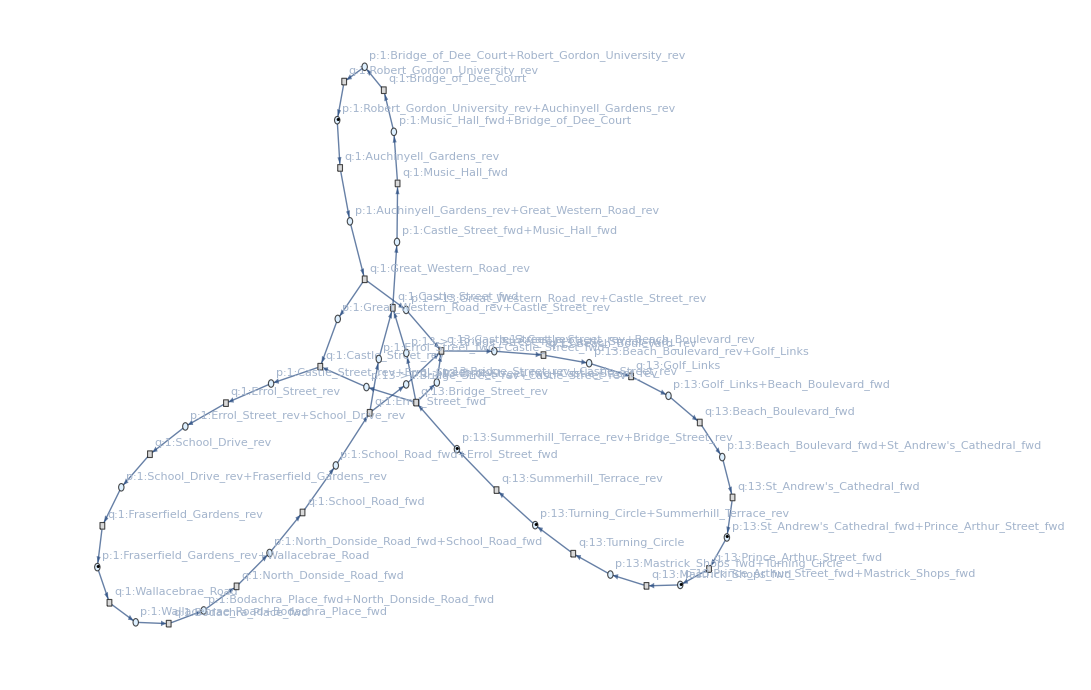

```mathematica
petriNet["LabeledGraph"]
```